## Test feasibility of posterior model for TARDIS

## Poisson posterior predictive approaches a Gaussian

```mathematica
PoissonPostPred=ProbabilityDistribution[ni!(2(Ni+ni))!/(2^(Ni+ni+1/2)4^Ni Ni!(2ni)!(Ni+ni)!),{Ni,0,∞,1},Assumptions->{ni>0}];
PNgivenn[Ni_,ni_]:=Pochhammer[Ni+ni+1,Ni+ni]/(Pochhammer[ni+1,ni] 2^(3Ni+ni+1/2)Ni!)
CharacteristicFunction[NormalDistribution[μ,σ],t]
CharacteristicFunction[PoissonPostPred,t]
{Mean[PoissonPostPred],Variance[PoissonPostPred]}//FullSimplify
(*Assuming[{ni>0,Ni>0},Solve[D[PNgivenn[Ni,ni],Ni]==0,Ni]]*)
```

ⅇ^(ⅈ t μ-(t^2 σ^2)/2)

(2-ⅇ^(ⅈ t))^(-1/2-ni)

{1/2+ni,1+2 ni}

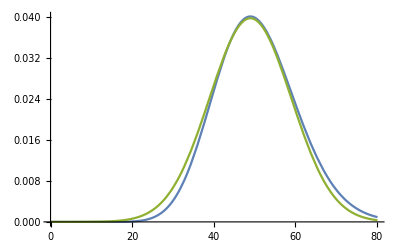

```mathematica
Module[{ni=50,σ},
σ=√(2ni+1);Plot[{PNgivenn[Ni,ni],PDF[PoissonPostPred[ni],Ni],PDF[NormalDistribution[ni-1,σ],Ni]},{Ni,0,ni+3σ}]
]
```

```mathematica
Assuming[k ∈Integers&& k>0,PNgivenn[n-1,n]/PNgivenn[n-1+k,n]//FullSimplify]
PNgivenn[n-1,n]/PNgivenn[n-2,n]//FullSimplify
```

(2^k Gamma[k+n] Gamma[-1/2+2 n])/(Gamma[n] Gamma[-1/2+k+2 n])

1+1/(4 (-1+n))

```mathematica
Limit[PNgivenn[Ni,ni],ni-> ∞]
```

0

Trying to estimate mean and variance of asymptotic Gaussian. No success!

```mathematica
Normal[Series[Log[PNgivenn[Ni,ni]],{ni,Infinity,1}]]/.{x_!-> x Log[x]-x}//FullSimplify
```

(Ni (1+3 Ni))/(4 ni)-ni Log[2]-Ni Log[1/ni]+Log[2^(-1/2-2 Ni)/(Ni (-1+Log[Ni]))]

```mathematica
Normal[-Log[2] ni+(-Ni Log[1/ni]+Log[2^(-1/2-2 Ni)/(-Ni+Ni Log[Ni])])+(Ni+3 Ni^2)/(4 ni)+O[1/ni]^2]
```

(Ni+3 Ni^2)/(4 ni)-ni Log[2]-Ni Log[1/ni]+Log[2^(-1/2-2 Ni)/(-Ni+Ni Log[Ni])]

```mathematica
Series[(2-ⅇ^(ⅈ t))^(-1/2-n),{n,∞,1}]
```

(2-ⅇ^(ⅈ t))^(-1/2-n)

No packet seen is also information

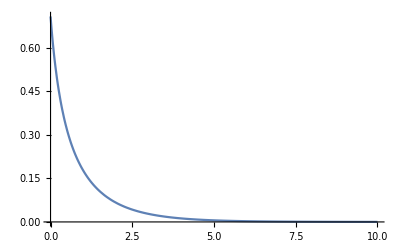

1

```mathematica
Plot[PNgivenn[Ni,0],{Ni,0,10},PlotRange->Full]
Sum[PNgivenn[Ni,0],{Ni,0,∞}]
```

## Some luminosity samples from real packets

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"samples.dat"}],samples,"List"]*)
```

```mathematica
samples=ReadList[FileNameJoin[{NotebookDirectory[],"samples.dat"}]];
```

Triweight kernel falls off quicker so at sharp edge, less probability spills over

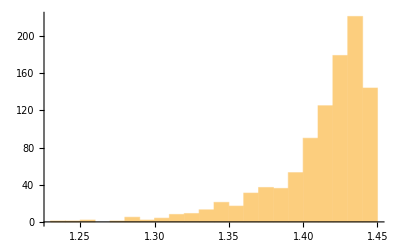

```mathematica
Histogram[samples]
dist=SmoothKernelDistribution[samples,"Oversmooth","Triweight"];
f=PDF[dist,l]; F=CDF[dist,l];
```

Determine central 99% interval

FindMaximum::fmdig: Working precision MachinePrecision is insufficient to achieve the requested accuracy or precision.

1.43881

1.27969

1.44908

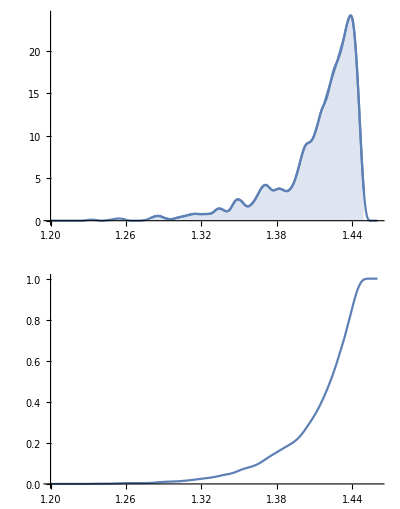

```mathematica
FindMaximum[f,{l,1.4}][[2,1,2]]
lmin=FindRoot[F==1-0.995,{l,1.3}][[1,2]]
lmax=FindRoot[F==0.995,{l,1.45}][[1,2]]
GraphicsColumn[{Show[Plot[f,{l,1.20,1.46},PlotRange->Full],Plot[f,{l,lmin,lmax},PlotRange->Full,Filling->Axis]],Plot[F,{l,1.20,1.46},PlotRange->Full]}]
```

Automatic results not too bad but still significantly off to the right of the peak

{WeibullDistribution[68.138,1.4254],MixtureDistribution[{0.198203,0.801797},{LogisticDistribution[1.40344,0.0378716],NormalDistribution[1.42458,0.0141769]}],StudentTDistribution[1.42196,0.017178,2.07419]}

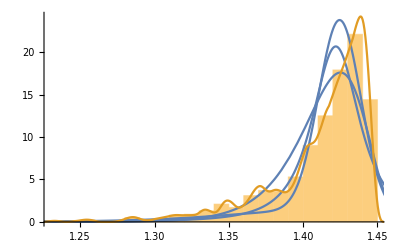

```mathematica
dists=FindDistribution[samples,3]
Show[Histogram[samples, "Scott", "PDF"],Plot[{PDF[#,L]&/@dists,PDF[dist,L]},{L,1.2,1.46}]]
```

Upper limit has to be enlarged beyond 2*99% limit

```mathematica
PLgivenN2=ParallelTable[{L,NIntegrate[PDF[dist,L-l]PDF[dist,l],{l,1.19,1.49}]},{L,2lmin,2lmax+0.1,0.02}]
PLgivenN2=Cases[PLgivenN2,{x_,y_}/;y≥ 0];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in l near {l} = {1.43785}. NIntegrate obtained 0.376719 and 0.000012115 for the integral and error estimates.

{{2.55939,0.00586915},{2.57939,0.0127373},{2.59939,0.0296357},{2.61939,0.0533618},{2.63939,0.100035},{2.65939,0.22191},{2.67939,0.376719},{2.69939,0.591199},{2.71939,1.04516},{2.73939,1.54613},{2.75939,2.42349},{2.77939,3.68849},{2.79939,5.0663},{2.81939,6.72886},{2.83939,9.95558},{2.85939,11.4977},{2.87939,6.81804},{2.89939,0.0283326},{2.91939,-9.53261×10^-17},{2.93939,-1.35821×10^-17},{2.95939,-1.78658×10^-33},{2.97939,-3.65114×10^-34}}

Build sequence of 1D integrals. Can’t go beyond linear interpolation to guarantee nonnegative values. Compare to sum of consecutive samples where I take only every 2nd element to have uncorrelated samples.

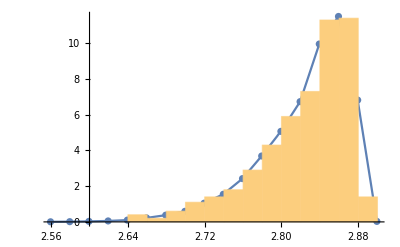

```mathematica
PLgivenNinter2=Interpolation[PLgivenN2,InterpolationOrder->1];
Show[Plot[PLgivenNinter2[L],{L,PLgivenN2[[1,1]],Last[PLgivenN2][[1]]}],ListPlot[PLgivenN2],Histogram[Take[ListConvolve[{1,1},samples],{1,-1,2}],"Scott","PDF"]]
```

Strange: some values are negative!

```mathematica
PLgivenN3=ParallelTable[{L,NIntegrate[PLgivenNinter2[L-l]PDF[dist,l],{l,1.19,1.49}]},{L,3 lmin,3lmax+0.1,0.02}]
PLgivenN3=Cases[PLgivenN3,{x_,y_}/;y≥ 0];
PLgivenNinter3=Interpolation[PLgivenN3,InterpolationOrder->1];
```

{{3.83908,-0.0395307},{3.85908,-0.0326},{3.87908,-0.0255401},{3.89908,-0.018179},{3.91908,-0.010241},{3.93908,-0.00105898},{3.95908,0.0105592},{3.97908,0.0265311},{3.99908,0.0510442},{4.01908,0.0908991},{4.03908,0.156109},{4.05908,0.261688},{4.07908,0.433384},{4.09908,0.688701},{4.11908,1.04258},{4.13908,1.54042},{4.15908,2.20801},{4.17908,3.04619},{4.19908,4.07555},{4.21908,5.13076},{4.23908,6.03483},{4.25908,6.67812},{4.27908,6.28174},{4.29908,3.19574},{4.31908,-2.65275},{4.33908,-9.38305},{4.35908,-16.1728},{4.37908,-22.9625},{4.39908,-29.7522},{4.41908,-36.5419},{4.43908,-43.3316}}

InterpolatingFunction::dmval: Input value {3.90001} lies outside the range of data in the interpolating function. Extrapolation will be used.

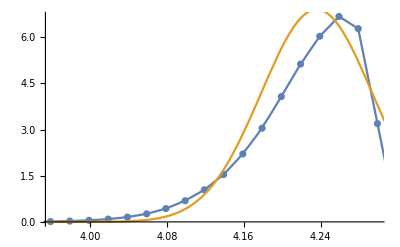

```mathematica
Show[ListPlot[PLgivenN3],Plot[{PLgivenNinter3[L],PDF[NormalDistribution[3 Mean[samples],Sqrt[3Variance[samples]]],L]},{L,3.9,4.4}]]
```

```mathematica
PLgivenN4=ParallelTable[{L,NIntegrate[PLgivenNinter3[L-l]PDF[dist,l],{l,1.19,1.49},Method->{"GlobalAdaptive",Method->"TrapezoidalRule"}]},{L,4 lmin,4lmax+0.1,0.02}]
PLgivenN4=Cases[PLgivenN4,{x_,y_}/;y≥ 0];
PLgivenNinter4=Interpolation[PLgivenN4,InterpolationOrder->1];
```

{{5.11877,-0.190909},{5.13877,-0.174937},{5.15877,-0.158965},{5.17877,-0.142993},{5.19877,-0.127021},{5.21877,-0.111046},{5.23877,-0.0950521},{5.25877,-0.0790063},{5.27877,-0.062829},{5.29877,-0.0463582},{5.31877,-0.0292645},{5.33877,-0.0109286},{5.35877,0.00979741},{5.37877,0.0348839},{5.39877,0.0678508},{5.41877,0.115268},{5.43877,0.187228},{5.45877,0.295435},{5.47877,0.455006},{5.49877,0.684274},{5.51877,1.00048},{5.53877,1.41576},{5.55877,1.94202},{5.57877,2.57935},{5.59877,3.3029},{5.61877,4.04875},{5.63877,4.69484},{5.65877,5.05363},{5.67877,4.92859},{5.69877,4.0087},{5.71877,1.92844},{5.73877,-1.08183},{5.75877,-4.16782},{5.77877,-7.25381},{5.79877,-10.3398},{5.81877,-13.4258},{5.83877,-16.5118},{5.85877,-19.5978},{5.87877,-22.6838}}

The integration goes awry and takes much longer than KDE of 125 samples. Additionally, the samples approach automatically tells us where probability is negligible. The integrals go far into the negative, that’s not what I want.

InterpolatingFunction::dmval: Input value {5.34001} lies outside the range of data in the interpolating function. Extrapolation will be used.

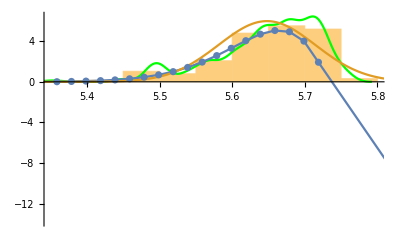

```mathematica
Show[Histogram[Take[ListConvolve[Table[1,{i,4}],samples],{1,-1,4}],"Scott","PDF"],SmoothHistogram[Take[ListConvolve[Table[1,{i,4}],samples],{1,-1,4}],{"Oversmooth","Triweight"},"PDF",PlotStyle->Green],Plot[{PLgivenNinter4[L],PDF[NormalDistribution[4 Mean[samples],Sqrt[4Variance[samples]]],L]},{L,5.34,5.87},PlotRange->Full],ListPlot[PLgivenN4]]
```

General solution with sum of N_i terms but not integration. Seems that even for 15, it is not symmetric but the Gaussian seems to be a good approximation even for 5 terms.

```mathematica
empiricalDist[Ni_]:=Module[{sums},
sums=Take[ListConvolve[Table[1,{i,Ni}],samples],{1,-1,Ni}]; (* uncorrelated *)
SmoothKernelDistribution[sums,"Oversmooth","Triweight"]
]
```

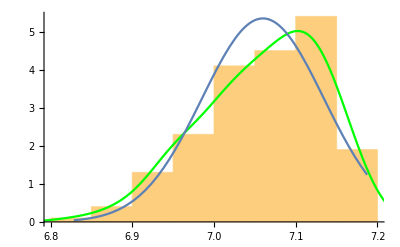

```mathematica
With[{Ni=5},
sums=Take[ListConvolve[Table[1,{i,Ni}],samples],{1,-1,Ni}]; (* uncorrelated *)
(* sums=ListConvolve[Table[1,{i,Ni}],samples]; *)(*correlated*)
Show[
Histogram[sums,"Scott","PDF"],SmoothHistogram[sums,{"LeastSquaresCrossValidation","Gaussian"},"PDF",PlotStyle->Green],Plot[PDF[NormalDistribution[Ni Mean[samples],Sqrt[Ni Variance[samples]]],L],{L,Min[sums],Max[sums]},PlotRange->Full]]
]
```

## Discrete sum related to Gaussian

```mathematica
P[L_,n_,mean_, var_]:=Module[{},Sum[PDF[NormalDistribution[Ni mean, √(Ni var)],L] PDF[NormalDistribution[n-1,√(2 n+1)],Ni],{Ni,1,150}]]
```

Result is a mixture distribution with weight given by Poisson posterior predictive. As many components/modes as there are summands. That’s a nasty function.

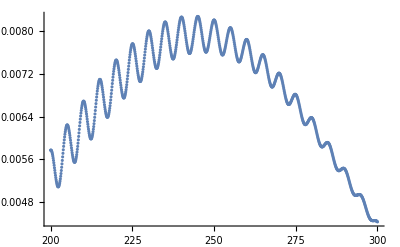

```mathematica
PL=ParallelTable[{L,P[L,50,5,0.1]},{L,200,300,0.1}];
ListPlot[PL]
```

Product of two Gaussians is Gaussian times a normalization that is also a Gaussian, see for example http://www.johndcook.com/blog/2012/10/29/product-of-normal-pdfs/
But for us it’s slightly more complicated: the two Gaussians are not for the same variable. I give up after staring at these equations for an hour.

```mathematica
Expand[-(1-n+Ni)^2/(2+4 n)-(L-mean Ni)^2/(2 Ni var)];
-(Expand[2 Ni var(1-n+Ni)^2+(2+4 n)(L-mean Ni)^2]/((2+4 n)(2 Ni var)))
```

-1/(2 (2+4 n) Ni var)(2 L^2+4 L^2 n-4 L mean Ni-8 L mean n Ni+2 mean^2 Ni^2+4 mean^2 n Ni^2+2 Ni var-4 n Ni var+2 n^2 Ni var+4 Ni^2 var-4 n Ni^2 var+2 Ni^3 var)

```mathematica
-Expand[Subscript[σ, 2]^2(x-Subscript[μ, 1])^2+Subscript[σ, 1]^2(x-Subscript[μ, 2])^2]/(2 Subscript[σ, 1]^2 Subscript[σ, 2]^2)
```

-(x^2 σ_1^2-2 x μ_2 σ_1^2+μ_2^2 σ_1^2+x^2 σ_2^2-2 x μ_1 σ_2^2+μ_1^2 σ_2^2)/(2 σ_1^2 σ_2^2)

```mathematica
x^2 Subscript[σ, 1]^2-2 x Subscript[μ, 2] Subscript[σ, 1]^2+x^2 Subscript[σ, 2]^2-2 x Subscript[μ, 1] Subscript[σ, 2]^2
```

Exchange sum and integral and first integrate over triple product of Gaussians

```mathematica
Integrate[PDF[NormalDistribution[μ,σ],L]PDF[NormalDistribution[Ni mean, √(Ni var)],L] PDF[NormalDistribution[n-1,√(2 n+1)],Ni],{L,0,∞},Assumptions->{Ni>0&& var>0 &&σ>0}]
```

(ⅇ^(-(mean^2 (1+2 n) Ni^2+Ni^3 var-2 mean (1+2 n) Ni μ+μ^2+2 n μ^2+σ^2-2 n σ^2+n^2 σ^2+(-1+n) Ni ((-1+n) var-2 σ^2)+Ni^2 (-2 (-1+n) var+σ^2))/(2 (1+2 n) (Ni var+σ^2))) (√((var μ+mean σ^2)^2)+(var μ+mean σ^2) Erf[(√((Ni (var μ+mean σ^2)^2)/(var (Ni var+σ^2))))/(√2 σ)]))/(4 π √((1+2 n) (Ni var+σ^2)) √((var μ+mean σ^2)^2))

```mathematica
tripleProd[μ_,σ_,Ni_,n_,mean_,var_]:=(ⅇ^(-(mean^2 (1+2 n) Ni^2+Ni^3 var-2 mean (1+2 n) Ni μ+μ^2+2 n μ^2+σ^2-2 n σ^2+n^2 σ^2+(-1+n) Ni ((-1+n) var-2 σ^2)+Ni^2 (-2 (-1+n) var+σ^2))/(2 (1+2 n) (Ni var+σ^2))) (√((var μ+mean σ^2)^2)+(var μ+mean σ^2) Erf[(√((Ni (var μ+mean σ^2)^2)/(var (Ni var+σ^2))))/(√2 σ)]))/(4 π √((1+2 n) (Ni var+σ^2)) √((var μ+mean σ^2)^2))
```

Approximate sum by integral. No analytic result but numerical integration gives same number. Safe to cut off some region away from the mode. Very nice! If integration over [0,∞] is too slow, should be enough to sum over +- 3 √(2n+1) (rounded to integers) as an estimate. For large n, the function is symmetric, so the lower tail is sufficient assuming there enough zero values at the density doesn’t reach near the origin.

0.0479378

0.0479378

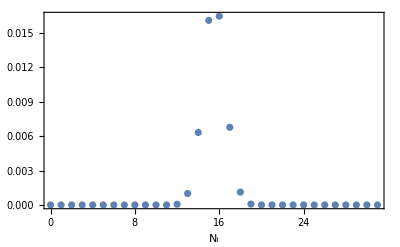

{{0,7.85783×10^-51},{1,1.61812×10^-44},{2,6.56883×10^-39},{3,1.05279×10^-33},{4,6.67042×10^-29}}

```mathematica
Module[{μ=22,σ=1.5,n=15,mean=Mean[samples],var=Variance[samples],width},
width=√(2n+1);
PDgivenN=Table[{Ni,tripleProd[μ,σ,Ni,n,mean,var]},{Ni,⌊Max[0,n-3.width]⌋,⌊n+3width⌋}];
NIntegrate[tripleProd[μ,σ,Ni,n,mean,var],{Ni,0,∞}]
]
Total[PDgivenN][[2]]
ListPlot[PDgivenN,PlotRange->Full,FrameLabel->{Subscript[N, i],""}, Frame->True]
PDgivenN[[1;;5]]
```

How does the width of PDgivenN depend on the parameters? It would help us find a suitable cut off. 
The mode is still near n so we could grow outward from there until remaining terms are too small.
Increasing var, n, or σ increases the width. Looking at the denominator of the exponent of tripleProd, it is a Gaussian with variance (2n+1)(N_i var + σ^2). Of course the numerator is not that of a Gaussian but it makes sense that the variance is proportional to n and depends on the relative size of N_i var and σ. As usual, relative uncertainty goes down like 1/√n

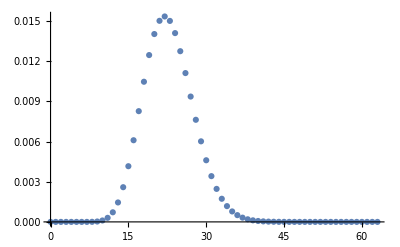

Mathematica not clever enough to simplify.

```mathematica
Simplify[tripleProd[μ,σ,Ni,n,mean,var],Assumptions->{σ>0,μ∈Reals,Ni>0,n>0,mean>0,var>0}]/.{mean->"E",var->"V"}
```

(ⅇ^(-(E^2 (1+2 n) Ni^2+V Ni^3-2 E (1+2 n) Ni μ+μ^2+2 n μ^2+σ^2-2 n σ^2+n^2 σ^2+(-1+n) Ni (V (-1+n)-2 σ^2)+Ni^2 (-2 V (-1+n)+σ^2))/(2 (1+2 n) (V Ni+σ^2))) (Abs[V μ+E σ^2]+(V μ+E σ^2) Erf[Abs[V μ+E σ^2]/(√2 σ √((V (V Ni+σ^2))/Ni))]))/(4 π √((1+2 n) (V Ni+σ^2)) Abs[V μ+E σ^2])

```mathematica
Limit[tripleProd[μ,σ,Ni,n,mean,var],{Ni->0}]
```

```mathematica
With[{μ=5,σ=0.5,n=15},{(ⅇ^(-(-1+n)^2/(2+4 n)-μ^2/(2 σ^2)))/(4 π √((1+2 n) σ^2))}]
```

{2.33606×10^-25}

```mathematica
With[{μ=5}, μ]
```

5

```mathematica
Simplify[ⅇ^(-(("E")^2 (1+2 n) Ni^2+"V" Ni^3-2 "E" (1+2 n) Ni μ+μ^2+2 n μ^2+σ^2-2 n σ^2+n^2 σ^2+(-1+n) Ni ("V" (-1+n)-2 σ^2)+Ni^2 (-2 "V" (-1+n)+σ^2))/(2 (1+2 n) ("V" Ni+σ^2)))]
```

ⅇ^(-(E^2 (1+2 n) Ni^2+V Ni (1-n+Ni)^2-2 E (1+2 n) Ni μ+μ^2+2 n μ^2+σ^2-2 n σ^2+n^2 σ^2+2 Ni σ^2-2 n Ni σ^2+Ni^2 σ^2)/(2 (1+2 n) (V Ni+σ^2)))

We don’t need the triple product: just a product of two Gaussians, because the integral is the well known convolution of two Gaussians for the same variable.

```mathematica
FullSimplify[Log[PDF[NormalDistribution[Ni mean, √(Ni var+σ^2)],μ] PDF[NormalDistribution[n-1,√(2 n+1)],Ni]],Assumptions->{σ>0&&μ>0&&Ni>0&&n>0&&mean>0&&var>0}]
```

-(1-n+Ni)^2/(2+4 n)-(-mean Ni+μ)^2/(2 (Ni var+σ^2))-Log[2 π]-1/2 Log[(1+2 n) (Ni var+σ^2)]

There are 4 solutions, pick out the only real solution

```mathematica
logProd=-(1-n+Ni)^2/(2+4 n)-(-mean Ni+μ)^2/(2 (Ni var+σ^2))-Log[2 π]-1/2 Log[(1+2 n) (Ni var+σ^2)];
Solve[D[logProd,Ni]==0,Ni][[1]]//Simplify
```

{Ni→-1/(6 var^2)(mean^2 var+2 mean^2 n var+2 var^2-2 n var^2+4 var σ^2+(var^2 (mean^4 (1+2 n)^2+(-2-20 n+4 n^2) var^2+8 (-1+n) var σ^2+4 σ^4-4 mean^2 (1+2 n) ((-1+n) var+σ^2)))/(mean^6 var^3+6 mean^6 n var^3+12 mean^6 n^2 var^3+8 mean^6 n^3 var^3+6 mean^4 var^4+18 mean^4 n var^4-24 mean^4 n^3 var^4+3 mean^2 var^5-36 mean^2 n var^5-72 mean^2 n^2 var^5+24 mean^2 n^3 var^5-10 var^6-42 n var^6+60 n^2 var^6-8 n^3 var^6-54 var^5 μ^2-108 n var^5 μ^2-6 mean^4 var^3 σ^2-24 mean^4 n var^3 σ^2-24 mean^4 n^2 var^3 σ^2-24 mean^2 var^4 σ^2-24 mean^2 n var^4 σ^2+48 mean^2 n^2 var^4 σ^2-6 var^5 σ^2+84 n var^5 σ^2-24 n^2 var^5 σ^2-108 mean var^4 μ σ^2-216 mean n var^4 μ σ^2-42 mean^2 var^3 σ^4-84 mean^2 n var^3 σ^4+24 var^4 σ^4-24 n var^4 σ^4-8 var^3 σ^6+√(var^6 ((-mean^4 (1+2 n)^2+(2+20 n-4 n^2) var^2-8 (-1+n) var σ^2-4 σ^4+4 mean^2 (1+2 n) ((-1+n) var+σ^2))^3+(mean^6 (1+2 n)^3-108 mean (1+2 n) var μ σ^2-6 mean^4 (1+2 n)^2 ((-1+n) var+σ^2)+3 mean^2 (1+2 n) ((1-14 n+4 n^2) var^2+8 (-1+n) var σ^2-14 σ^4)-2 ((5+21 n-30 n^2+4 n^3) var^3+12 (-1+n) var σ^4+4 σ^6+3 var^2 (9 (1+2 n) μ^2+(1-14 n+4 n^2) σ^2)))^2)))^(1/3)+(mean^6 var^3+6 mean^6 n var^3+12 mean^6 n^2 var^3+8 mean^6 n^3 var^3+6 mean^4 var^4+18 mean^4 n var^4-24 mean^4 n^3 var^4+3 mean^2 var^5-36 mean^2 n var^5-72 mean^2 n^2 var^5+24 mean^2 n^3 var^5-10 var^6-42 n var^6+60 n^2 var^6-8 n^3 var^6-54 var^5 μ^2-108 n var^5 μ^2-6 mean^4 var^3 σ^2-24 mean^4 n var^3 σ^2-24 mean^4 n^2 var^3 σ^2-24 mean^2 var^4 σ^2-24 mean^2 n var^4 σ^2+48 mean^2 n^2 var^4 σ^2-6 var^5 σ^2+84 n var^5 σ^2-24 n^2 var^5 σ^2-108 mean var^4 μ σ^2-216 mean n var^4 μ σ^2-42 mean^2 var^3 σ^4-84 mean^2 n var^3 σ^4+24 var^4 σ^4-24 n var^4 σ^4-8 var^3 σ^6+√(var^6 ((-mean^4 (1+2 n)^2+(2+20 n-4 n^2) var^2-8 (-1+n) var σ^2-4 σ^4+4 mean^2 (1+2 n) ((-1+n) var+σ^2))^3+(mean^6 (1+2 n)^3-108 mean (1+2 n) var μ σ^2-6 mean^4 (1+2 n)^2 ((-1+n) var+σ^2)+3 mean^2 (1+2 n) ((1-14 n+4 n^2) var^2+8 (-1+n) var σ^2-14 σ^4)-2 ((5+21 n-30 n^2+4 n^3) var^3+12 (-1+n) var σ^4+4 σ^6+3 var^2 (9 (1+2 n) μ^2+(1-14 n+4 n^2) σ^2)))^2)))^(1/3))}

For Laplace approximation, need Hessian. Differs in the third digit only!

```mathematica
parValues={μ-> 5 1.41,σ->3,n->5,var-> Variance[samples],mean->Mean[samples]};

f=PDF[NormalDistribution[Ni mean, √(Ni var+σ^2)],μ] PDF[NormalDistribution[n-1,√(2 n+1)],Ni];
Solve[D[f,Ni]==0,Ni][[1]]/.parValues
{f √((2 Pi)/(-D[logProd,{Ni,2}]))/.parValues/.%//Re,NIntegrate[f/.parValues,{Ni,0,∞}]}
```

{Ni→4.70376}

{0.0694818,0.0691846}

## Compute the luminosity integral for general case including small n

Agreement with Gaussian approx. 
n=1: 0.103 (general) vs. 0.097(Gaussian) (Laplace not usable anymore)
n=3: 0.106 (general) vs. 0.0930(Gaussian) (Laplace differs in 3rd digit)
n=5: 0.0846 (general) vs. 0.0779(Gaussian)
n=10: 0.0613 (general) vs. 0.0587(Gaussian)
n=15: 0.0505 (general) vs. 0.0491 (Gaussian)
n=35: 0.03237 (general) vs. 0.03197 (Gaussian)
n=100: 0.019839 (general) vs. 0.019842 (Gaussian)

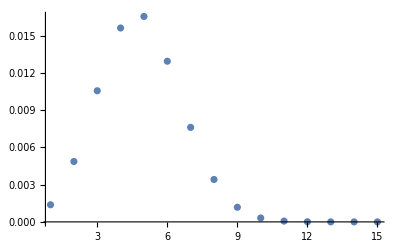

0.0745867

```mathematica
data=ParallelTable[{Ni,NIntegrate[PDF[empiricalDist[Ni],L]PNgivenn[Ni,n] PDF[NormalDistribution[μ,σ],L]/.parValues,{L,0,∞}]},{Ni,1,15}];
ListPlot[data,PlotRange->All]
Total[data][[2]]
```

NIntegrate is slow, replace with Laplace. Not useful because derivative of KDE not well known